# Dipolar Interaction

## Gabriel Patenotte Ni Lab

### Versions

v05022023: cleaned up the code for Git.

### Setup

Choosing default plot options, turning off warnings, and picking a color scheme.

```mathematica
SetDirectory["/Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica"];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImageSize->500,AxesLabel->{"",""}]; 
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImageSize->500,AxesLabel->{"",""}]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
colors=RGBColor/@{"#408EC6","#7A2048","#1E2761","#89ABE3FF","#EA738DFF","#8BB9B9"};
```

#### Basis labels

Defining the quantum numbers for different bases. In this code, only bN is relevant.

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN","S","mS"};
bI={"I1","I2","I","mI","N","mN","S","mS"};
bJ={"I1","mI1","I2","mI2","N","S","J","mJ"};
bIJ={"I1","I2","I","mI","N","S","J","mJ"};
bF={"I1","I2","I","N","S","J","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1","S","J"};
bF2={"I1","mI1","I2","N","F2","mF2","S","J"};
bN={"N","mN"};
bI1={"I1","mI1"};
bI2={"I2","mI2"};
bS={"S","mS"};
b={bUC,bI,bJ,bIJ,bF,bF1,bF2,bN};
```

#### Supporting functions

createSpace creates a matrix that represents the molecular Hilbert space, and vectors that represent eigenstates in the Hilbert space.

```mathematica
conj[x_]:=Module[{re,im},x/.(Complex[re_,im_]->Complex[re,-im])]; (*Replacement that gives the complex conjugate*)
createSpace[aQN_Association]:=Module[{a},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
nℋ=Sum[(2I1+1)(2I2+1)(2N+1)(2S+1),{N,a["N"]},{S,a["S"]},{I1,a["I1"]},{I2,a["I2"]}]; (*number of states in Hilbert space*)
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
nℋI1=(2a["I1"][[1]]+1);
nℋI2=(2a["I2"][[1]]+1);
nℋI=(2a["I1"][[1]]+1)(2a["I2"][[1]]+1);
nℋS=(2a["S"][[1]]+1);
nℋN=Sum[(2N+1),{N,a["N"]}];
ℋ=IdentityMatrix[nℋ];
ℋI1=IdentityMatrix[nℋI1];
ℋI2=IdentityMatrix[nℋI2];
ℋI=IdentityMatrix[nℋI];
ℋS=IdentityMatrix[nℋS];
ℋN=IdentityMatrix[nℋN];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
sℋI1=Partition[ℋI1,{nℋI1,1}][[1]];
sℋI2=Partition[ℋI2,{nℋI2,1}][[1]];
sℋI=Partition[ℋI,{nℋI,1}][[1]];
sℋS=Partition[ℋS,{nℋS,1}][[1]];
sℋN=Partition[ℋN,{nℋN,1}][[1]];
] (*example: aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->{0,1}]*)
```

createLists creates lists of quantum numbers that describe the states in the Hilbert space.

```mathematica
createLists[aQN_Association]:=Module[{a,spins},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
am={{I1,a["I1"]},{I2,a["I2"]},{S,a["S"]},{N,a["N"]}}; (*angular momentums*)
lUC=Flatten[Table[ToExpression[bUC],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{mS,-S,S},{mN,-N,N}],7];
lI=Flatten[Table[ToExpression[bI],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{mN,-N,N},{mS,-S,S}],7];
lJ=Flatten[Table[ToExpression[bJ],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lIJ=Flatten[Table[ToExpression[bIJ],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lF=Flatten[Table[ToExpression[bF],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{J,Abs[N-S],N+S},{F,Abs[I-J],I+J},{mF,-F,F}],7];
lF1=Flatten[Table[ToExpression[bF1],Evaluate[Sequence@@am],{mI2,-I2,I2},{J,Abs[N-S],N+S},{F1,Abs[I1-J],I1+J},{mF1,-F1,F1}],7];
lF2=Flatten[Table[ToExpression[bF2],Evaluate[Sequence@@am],{mI1,-I1,I1},{J,Abs[N-S],N+S},{F2,Abs[I2-J],I2+J},{mF2,-F2,F2}],7];
lN=Flatten[Table[ToExpression[bN],{N,a["N"]},{mN,-N,N}],1];
l = {lUC,lI,lJ,lIJ,lF,lF1,lF2,lN};
BtoL = AssociationThread[b->l];
LtoB = AssociationThread[l->b];
yN=lN/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
]
```

### Functions

```mathematica
eig[Hn_]:=Chop[Sort[Eigensystem[Hn]ᵀ]ᵀ];
reorder[list_,order_]:=Part[order,list];
VtoQN[eigenvector_,basis_:bUC,populationThreshold_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eigenvector,Abs[#]^2>=populationThreshold&],Abs];
sP=Position[eigenvector,#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,BtoL[basis][[sP]]}]
QNtoS[rep_,basis_:bUC]:=With[{labels=rep[[All,1]],numbers=rep[[All,2]]},Flatten[Position[BtoL[basis][[All,Flatten[labels/.PositionIndex[basis]]]],numbers]]]
QNtoV[rep_,eigenvectors_,basis_:bUC]:=Module[{pos,eigs},pos=QNtoS[rep];eigs=OrderingBy[eigenvectors[[All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];eigs]
reduceV[vecs_,param_,s_,rep_]:=Module[{pos,l},
pos=Flatten[Position[bUC,#]&/@rep[[All,1]]];
l=Transpose@{lUC[[All,pos]],Abs[vecs[[param,s]]]^2};
l=Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[l,First]];
l[[All,2]]
]
```

### Load

```mathematica
aQN = Association["I1"->0, "I2"->0, "S"->0, "N"->Range[0,1]];
createSpace[aQN] (*creates a Hilbert space*)
createLists[aQN] (*creates a list of the quantum numbers of each basis state*)
```

```mathematica
HacN=Import["HacN.m"][[1;;nℋN,1;;nℋN]];
```

### Multiparticle

```mathematica
nP=2;
ℋn=IdentityMatrix[nℋN^nP];(*multi-particle Hilbert space*)
nℋn=Length[ℋn];(*number of states in the multi-particle Hilbert space*)
sℋn=Partition[ℋn,{nℋN^nP,1}][[1]];(*states in the multi-particle Hilbert space*)
lℋn=Flatten[Table[{{ni,mi},{nj,mj}},{ni,aQN["N"]},{mi,-ni,ni},{nj,aQN["N"]},{mj,-nj,nj}],3];(*multi-particle state labels |Subscript[N, i],Subscript[m, i]⟩|Subscript[N, j],Subscript[m, j]⟩*)
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
```

### Dipole-dipole interaction

```mathematica
dpME[q_,{Nb_,mb_},{Nk_,mk_}]:=Quiet[d0(-1)^mb √((2 Nb+1) (2 Nk+1)) ThreeJSymbol[{Nb,-mb},{1,q},{Nk,mk}] ThreeJSymbol[{Nb,0},{1,0},{Nk,0}]](*dipole matrix element for spherical component q between bra Nm and ket Nm*)
HddME[{b1_,b2_},{k1_,k2_}]:=Sum[-(√6)/(4π ϵ0 r^3 h)(-1)^(2-p)√((4π)/(2 2+1))SphericalHarmonicY[2,-p,θD,ϕD]Sum[dpME[p1,b1,k1]dpME[p-p1,b2,k2] √(2 2+1)ThreeJSymbol[{1,p1},{1,p-p1},{2,-p}](-1)^(-1+1-p),{p1,-1,1}],{p,-2,2}]
srDD[{{bn1_,bm1_},{bn2_,bm2_}},{{kn1_,km1_},{kn2_,km2_}}]:=Abs[kn1-kn2]==1∧Abs[bn1-bn2]==1
```

### Hamiltonians

```mathematica
HN=DiagonalMatrix[#(#+1)&/@lN[[All,1]]]; (*needs to be multiplied by B*)
H1=B HN+U HacN;
```

```mathematica
H20=KroneckerProduct[H1,ℋN]+KroneckerProduct[ℋN,H1];
```

```mathematica
Hdd=ParallelTable[If[srDD[lℋn[[i]],lℋn[[j]]],HddME[lℋn[[i]],lℋn[[j]]],0],{i,1,nℋn},{j,1,nℋn}];
```

```mathematica
H2=H20+Hdd;
```

```mathematica
rep={B->1.7396 10^9,αpar->1872.12,αperp->467.038,θq->(π/2-ArcCos[1/√3]),θh->0,U->10^6,d0->4.6/299792458000000000000000000000,r->5 10^-6,ϵ0->8.85418781280000060485535391`9.532175381914792*^-12,θD->π/2,ϕD->0,h->132521403/200000000000000000000000000000000000000000};
```

```mathematica
H2n=H2/.rep;
ψ0=FullSimplify[KroneckerProduct[Normalize[eig[H1][[2,3]]],sℋN[[1]]]/.rep];
ψ1=FullSimplify[KroneckerProduct[sℋN[[1]],{Normalize[eig[H1][[2,3]]]}ᵀ]/.rep];
```

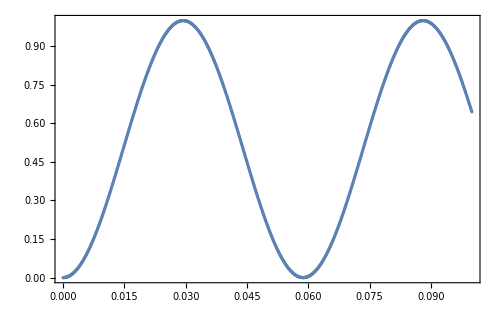

```mathematica
tab=ParallelTable[(Abs[ψ1†.MatrixExp[-2π ⅈ t H2n].ψ0]^2)[[1,1]],{t,0,10^-1,10^-4}];
ListPlot[tab,DataRange->{0,10^-1}]
```

### Polarization

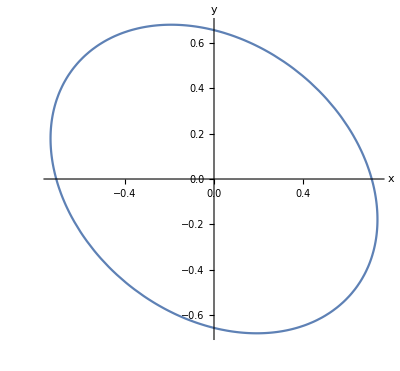

```mathematica
qwp[θ_]=Exp[-(ⅈ π)/4]({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ) Sin[θ]Cos[θ]}, {(1-ⅈ) Sin[θ]Cos[θ], Sin[θ]^2+ⅈ Cos[θ]^2}});(*quarter waveplate Jones matrix*)
hwp[θ_]=Exp[-(ⅈ π)/2]({{Cos[θ]^2-Sin[θ]^2, 2Cos[θ]Sin[θ]}, {2Cos[θ]Sin[θ], Sin[θ]^2-Cos[θ]^2}});(*half waveplate Jones matrix*)
lpr[η_,θ_]=Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ]}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2}});(*linear phase retarder Jones matrix*)

jH=({{1}, {0}});jV=({{0}, {1}});jL=1/(√2)({{1}, {ⅈ}});jR=1/(√2)({{1}, {-ⅈ}});(*Jones vectors for horizontal, vertical, LCP, and RCP light*)
jF[θh_,θq_]=FullSimplify[Flatten[hwp[θh].qwp[θq].jH],Assumptions->{0<=θh<2π,0<=θq<2π}];(*Jones vector seen by molecules*)

pEllipse[θh_,θq_]=FullSimplify[ComplexExpand[Re[jF[θh,θq]Exp[-ⅈ t]]],Assumptions->{t>0,0<=θh<2π,0<=θq<2π}];
ParametricPlot[pEllipse[θh,θq]/.rep,{t,0,2π},AxesLabel->{"x","y"}]
```

```mathematica
180/π(π/2-ArcCos[1/√3])//N
180/π(ArcCos[1/√3])//N
```

35.2644

54.7356

```mathematica
(1-3 Cos[θ]^2)/.θ->π/2-ArcCos[1/√3]
(1-3 Cos[θ]^2)/.θ->ArcCos[1/√3]
```

-1

0

```mathematica
ArcCos[1/√3] 180/π//N
```

54.7356